## Figure 4A

Phase plane analysis for comparing the well-mixed and spatial steady states. This code generates a plot for a single value of τ_D. For the paper, we used D=1, E=1, L=(0,5,10), yielding τ_D=(0,25,100).

```mathematica
Clear["Global`*"]; 
precision=30;
$MinPrecision=precision;
SetDirectory[NotebookDirectory[]];
```

### set system size

```mathematica
l=10;
```

### Statics

```mathematica
getPositions[pop0_]:=
Block[{m0,list,extendedPop},
m0=Length[pop0];
extendedPop=Join[{0},pop0];
Table[{Total[extendedPop[[1;;i-1]]],Total[extendedPop[[1;;i]]]},{i,2,m0+1}]
];

getConcentration[n_,nutrient_]:=
Block[{i,m0,c,dc,m,cSys,cSysWrap,cSystem,dcSys,dcSysWrap,dcSystem,totalcSys,vars,aVars,bVars,z},
m0=Length[n];
aVars=ToExpression[Table["a"<>IntegerString[k],{k,m0}]];
bVars=ToExpression[Table["b"<>IntegerString[k],{k,m0}]];
c[a_,b_,α_,θ_]:=a*E^(Sqrt[α/d]*θ)+b*E^(-Sqrt[α/d]*θ)+s[[nutrient]]/α;
dc[a_,b_,α_,θ_]:=Sqrt[α/d]*(a*E^(Sqrt[α/d]*θ)-b*E^(-Sqrt[α/d]*θ));

(*  Create a system of eqs for c(θ) in each region *)
cSys=Table[c[aVars[[i]],bVars[[i]],α[[i,nutrient]],n[[i]]]==c[aVars[[i+1]],bVars[[i+1]],α[[i+1,nutrient]],0],{i,m0-1}];
cSysWrap=c[aVars[[m0]],bVars[[m0]],α[[m0,nutrient]],n[[m0]]]==c[aVars[[1]],bVars[[1]],α[[1,nutrient]],0];
cSystem=Join[cSys,{cSysWrap}];

(*do the same thing for the derivatives of c(θ)*)
dcSys=Table[dc[aVars[[i]],bVars[[i]],α[[i,nutrient]],n[[i]]]==dc[aVars[[i+1]],bVars[[i+1]],α[[i+1,nutrient]],0],{i,m0-1}];
dcSysWrap=dc[aVars[[m0]],bVars[[m0]],α[[m0,nutrient]],n[[m0]]]==dc[aVars[[1]],bVars[[1]],α[[1,nutrient]],0];
dcSystem=Join[dcSys,{dcSysWrap}];

totalcSys=Join[cSystem,dcSystem];
vars=Table[{aVars[[i]],bVars[[i]]},{i,m0}]//Flatten;
{z,m}=CoefficientArrays[totalcSys,vars];
LinearSolve[m,-z]        
];
(*returns {a1,b1,a2,b2...}: in a region σ c_i=a*E^(a*θ/d)+b*E^(-a*θ/d)+si/αi. *)

fullConcentration[n_,nutrient_]:=
Block[{a,b,c,coeff,positions,pieces,conditions,fullC},
coeff=getConcentration[n,nutrient];
positions=getPositions[n];
a=Table[coeff[[2*i-1]],{i,m}];
b=Table[coeff[[2*i]],{i,m}];
c[a_,b_,α_,θ_]:=a*E^(Sqrt[α/d]*θ)+b*E^(-Sqrt[α/d]*θ)+s[[nutrient]]/α;
pieces=Table[c[a[[j]],b[[j]],α[[j,nutrient]],theta-positions[[j,1]]],{j,m}];
conditions=Table[positions[[i,1]]<theta<=positions[[i,2]],{i,m}];
fullC=Piecewise[Transpose[{pieces,conditions}]]
];
```

### Define some constants

```mathematica
supply=1;  (*total nutrient supply*)
δ=supply;
e=1;             (* total enzyme budget*)
steps=20000;
```

### Numeric parameters

```mathematica
d=1; //N(*diffusion coefficient*)

s1=0.5;
s2=supply-s1;
s={s1,s2};

SeedRandom[29];
alphas={.3,.65,.7};
α=Table[{alphas[[i]],e-alphas[[i]]},{i,Length[alphas]}];
```

```mathematica
m=Length[α];
strat=Table[α[[i,1]],{i,m}];   (*maps strategies to continuum of nutrient 1, nutrient 2*)
sScaled=(e/Total[s])*s[[1]];
```

### strategy plotting

```mathematica
colors=Table[ColorData[97,i],{i,m}];
p=Table[{Graphics[{EdgeForm[{Black}],FaceForm[colors[[i]]],Disk[]}],.05},{i,m}];
```

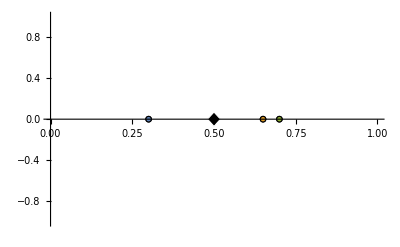

```mathematica
Show[ListPlot[Table[{{strat[[i]],0}},{i,m}],Axes->{True,False},AxesStyle->Thick,Ticks->{0,.2,.4,.6,.8,1},TicksStyle->Directive[Black, 12],PlotMarkers->p,PlotRange->{{0,1},Automatic}],Graphics[{EdgeForm[{White}],Polygon[{{.5-.02,0},{.5,.07},{.5+.02,0},{.5,-.07}}]}],Method->{"AxesInFront"->False}]
```

```mathematica
Export["fig4A_strategies.svg",%];
```

### simplex coordinate transformation

```mathematica
transform2Simplex[{n1_,n2_,n3_}]:=
Module[{},
{n2-n1,Sqrt[3]*n3}/l
]
```

### Dynamics

```mathematica
getGrowth[pop_,species_,c_]:=
Block[{growth,myN,myA,myB},
myN=pop[[species]];
myA=c[[species*2-1]];
myB=c[[species*2]];

growth=Table[α[[species,i]]*((s[[i]]*myN/α[[species,i]])+Sqrt[d/α[[species,i]]]*(myA[[i]]*(E^(myN*Sqrt[α[[species,i]]/d])-1)-myB[[i]]*(E^(-myN*Sqrt[α[[species,i]]/d])-1))),{i,2}]//Total
];
```

```mathematica
ndot[n_?(VectorQ[#, NumericQ]&)]:=
Block[{dn,growthTable,n0,nNew,cCoeff},
n0=n;
cCoeff=Transpose[{getConcentration[n0,1],getConcentration[n0,2]}];
growthTable=Table[getGrowth[n0,i,cCoeff],{i,Length[n0]}];
(*δ=Total[growthTable];*)
dn=growthTable-δ*n0
];

ndot2DSimplex[x_,y_]:=
(*for m=3, transforms coordinates to 2d simplex*)
Block[{dn,growthTable,n0,nNew,cCoeff},
(*transform back to real populations*)
n0=ConstantArray[0,3];
n0[[3]]=y*l/Sqrt[3];
n0[[2]]=.5*l*(1+x-y/Sqrt[3]);
n0[[1]]=n0[[2]]-l*x;

cCoeff=Transpose[{getConcentration[n0,1],getConcentration[n0,2]}];
growthTable=Table[getGrowth[n0,i,cCoeff],{i,Length[n0]}];
(*δ=Total[growthTable];*)
dn=growthTable-δ*n0;
(*return in simplex space*)
transform2Simplex[dn]
];
```

### Calculate spatial fixed points

```mathematica
randomInit[n_]:=RandomPoint[Simplex[l*IdentityMatrix[m]],n];
```

```mathematica
numTrials=40;
inits=randomInit[numTrials];
sols=ConstantArray[0,numTrials];
fixedPoints=ConstantArray[0,numTrials];
eigenSystems=ConstantArray[0,numTrials];
varList=Table["n"<>ToString[i]//ToExpression,{i,m}];
```

```mathematica
For[i=1,i≤numTrials,i++,
nInit=inits[[i]];
sol=NDSolveValue[{n'[t]==ndot[n[t]],n[0]==nInit},n,{t,0,steps}];
fixedPoints[[i]]=sol[steps];
sols[[i]]=sol;
];
```

### m=3 phase plane

### get colorscheme data

```mathematica
(*Read in the numerical data*)Get["https://pastebin.com/raw/gN4wGqxe"]
ParulaCM=With[{colorlist=RGBColor@@@parulaColors},Blend[colorlist,#]&];
Cube1CM=With[{colorlist=RGBColor@@@cube1Colors},Blend[colorlist,#]&];
CubeYFCM=With[{colorlist=RGBColor@@@cubeYFColors},Blend[colorlist,#]&];
LinearLCM=With[{colorlist=RGBColor@@@cube1Colors},Blend[colorlist,#]&];
JetCM=With[{colorlist=RGBColor@@@jetColors},Blend[colorlist,#]&];
```

### well-mixed solution

```mathematica
(*note that we scale supply by L to appropriately scale total population*)
```

```mathematica
wellMixedsols=Solve[{α[[1,1]]*(s1*l/(x*α[[1,1]]+y*α[[2,1]]+z*α[[3,1]]))+α[[1,2]]*(s2*l/(x*α[[1,2]]+y*α[[2,2]]+z*α[[3,2]]))==δ&&x+y+z==l},{x,y,z}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
wellMixedParametricFunction[x_]={x,y,z}/.wellMixedsols[[2]];
```

```mathematica
boundary=t/.Solve[wellMixedParametricFunction[t][[3]]==0,t];
```

### plot phase plane+spatial steady states+well-mixed steady states

```mathematica
(*normalize color scale by largest magnitude of derivative for the current tau_D*)
vectorList=Flatten[Table[ndot2DSimplex[x,y],{x,-1,1,.01},{y,0,Sqrt[3]*(1-Abs[x]),.01}],1];
vectorListNorm=Table[Norm[vectorList[[i]]],{i,Length[vectorList]}];
normMax=Max[vectorListNorm];
```

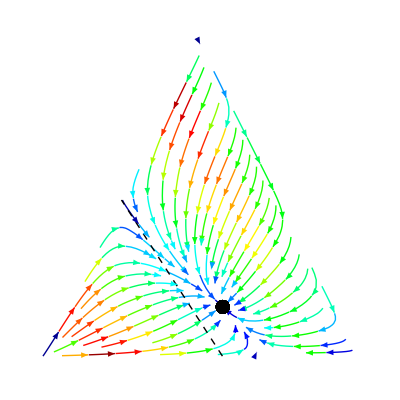

```mathematica
streamGraphic=Show[StreamPlot[{ndot2DSimplex[x,y]},{x,-1,1},{y,0,Sqrt[3]},StreamColorFunction->Function[{x,y,vx,vy,n},JetCM[n/normMax]],StreamColorFunctionScaling->False,RegionFunction->Function[{x,y},y<Sqrt[3]*(1-Abs[x])],Ticks->None,Frame->False],ListPlot[transform2Simplex/@fixedPoints,PlotStyle->Directive[Black,PointSize[.025]]],ParametricPlot[transform2Simplex[wellMixedParametricFunction[t]//Flatten],{t,10,boundary[[1]]},PlotStyle->Directive[Black,Thick,Dashed],RegionFunction->Function[{x,y},y<Sqrt[3]*(1-Abs[x])]]]
```

```mathematica
Export["fig4A_phasePlane.svg",streamGraphic];
```